# Analyzing Economic Trends: A Comparative Study of State-Space Models and Neural Networks

Muhammad Ali Hafeez

Abstract

## Introduction

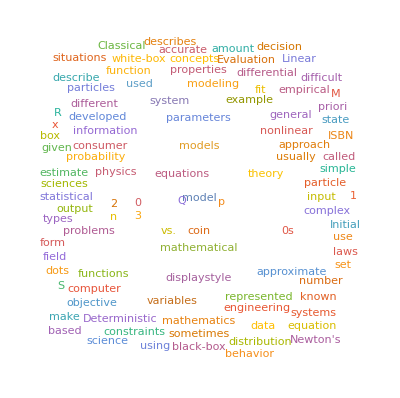

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->""; 
splitData=Partition[Flatten[preprocessedData],2];
table=Grid[splitData,Alignment->Center]//DisplayForm;
styledTable=StyleBox[table,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable=Pane[styledTable,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable
```

StyleBox[FRED Graph Observations | 
Federal Reserve Economic Data | 
Link: https://fred.stlouisfed.org | 
Help: https://fredhelp.stlouisfed.org | 
Economic Research Division | 
Federal Reserve Bank of St. Louis | 
 | 
GDP | Gross Domestic Product, Billions of Dollars, Quarterly, Seasonally Adjusted Annual Rate
 | 
Frequency: Quarterly | 
observation_date | GDP
Wed 1 Jan 1947 00:00:00GMT-4 | 243.164
Tue 1 Apr 1947 00:00:00GMT-4 | 245.968
Tue 1 Jul 1947 00:00:00GMT-4 | 249.585
Wed 1 Oct 1947 00:00:00GMT-4 | 259.745
Thu 1 Jan 1948 00:00:00GMT-4 | 265.742
Thu 1 Apr 1948 00:00:00GMT-4 | 272.567
Thu 1 Jul 1948 00:00:00GMT-4 | 279.196
Fri 1 Oct 1948 00:00:00GMT-4 | 280.366
Sat 1 Jan 1949 00:00:00GMT-4 | 275.034
Fri 1 Apr 1949 00:00:00GMT-4 | 271.351
Fri 1 Jul 1949 00:00:00GMT-4 | 272.889
Sat 1 Oct 1949 00:00:00GMT-4 | 270.627
Sun 1 Jan 1950 00:00:00GMT-4 | 280.828
Sat 1 Apr 1950 00:00:00GMT-4 | 290.383
Sat 1 Jul 1950 00:00:00GMT-4 | 308.153
Sun 1 Oct 1950 00:00:00GMT-4 | 319.945
Mon 1 Jan 1951 00:00:00GMT-4 | 336.
Sun 1 Apr 1951 00:00:00GMT-4 | 344.09
Sun 1 Jul 1951 00:00:00GMT-4 | 351.385
Mon 1 Oct 1951 00:00:00GMT-4 | 356.178
Tue 1 Jan 1952 00:00:00GMT-4 | 359.82
Tue 1 Apr 1952 00:00:00GMT-4 | 361.03
Tue 1 Jul 1952 00:00:00GMT-4 | 367.701
Wed 1 Oct 1952 00:00:00GMT-4 | 380.812
Thu 1 Jan 1953 00:00:00GMT-4 | 387.98
Wed 1 Apr 1953 00:00:00GMT-4 | 391.749
Wed 1 Jul 1953 00:00:00GMT-4 | 391.171
Thu 1 Oct 1953 00:00:00GMT-4 | 385.97
Fri 1 Jan 1954 00:00:00GMT-4 | 385.345
Thu 1 Apr 1954 00:00:00GMT-4 | 386.121
Thu 1 Jul 1954 00:00:00GMT-4 | 390.996
Fri 1 Oct 1954 00:00:00GMT-4 | 399.734
Sat 1 Jan 1955 00:00:00GMT-4 | 413.073
Fri 1 Apr 1955 00:00:00GMT-4 | 421.532
Fri 1 Jul 1955 00:00:00GMT-4 | 430.221
Sat 1 Oct 1955 00:00:00GMT-4 | 437.092
Sun 1 Jan 1956 00:00:00GMT-4 | 439.746
Sun 1 Apr 1956 00:00:00GMT-4 | 446.01
Sun 1 Jul 1956 00:00:00GMT-4 | 451.191
Mon 1 Oct 1956 00:00:00GMT-4 | 460.463
Tue 1 Jan 1957 00:00:00GMT-4 | 469.779
Mon 1 Apr 1957 00:00:00GMT-4 | 472.025
Mon 1 Jul 1957 00:00:00GMT-4 | 479.49
Tue 1 Oct 1957 00:00:00GMT-4 | 474.864
Wed 1 Jan 1958 00:00:00GMT-4 | 467.54
Tue 1 Apr 1958 00:00:00GMT-4 | 471.978
Tue 1 Jul 1958 00:00:00GMT-4 | 485.841
Wed 1 Oct 1958 00:00:00GMT-4 | 499.555
Thu 1 Jan 1959 00:00:00GMT-4 | 510.33
Wed 1 Apr 1959 00:00:00GMT-4 | 522.653
Wed 1 Jul 1959 00:00:00GMT-4 | 525.034
Thu 1 Oct 1959 00:00:00GMT-4 | 528.6
Fri 1 Jan 1960 00:00:00GMT-4 | 542.648
Fri 1 Apr 1960 00:00:00GMT-4 | 541.08
Fri 1 Jul 1960 00:00:00GMT-4 | 545.604
Sat 1 Oct 1960 00:00:00GMT-4 | 540.197
Sun 1 Jan 1961 00:00:00GMT-4 | 545.018
Sat 1 Apr 1961 00:00:00GMT-4 | 555.545
Sat 1 Jul 1961 00:00:00GMT-4 | 567.664
Sun 1 Oct 1961 00:00:00GMT-4 | 580.612
Mon 1 Jan 1962 00:00:00GMT-4 | 594.013
Sun 1 Apr 1962 00:00:00GMT-4 | 600.366
Sun 1 Jul 1962 00:00:00GMT-4 | 609.027
Mon 1 Oct 1962 00:00:00GMT-4 | 612.28
Tue 1 Jan 1963 00:00:00GMT-4 | 621.672
Mon 1 Apr 1963 00:00:00GMT-4 | 629.752
Mon 1 Jul 1963 00:00:00GMT-4 | 644.444
Tue 1 Oct 1963 00:00:00GMT-4 | 653.938
Wed 1 Jan 1964 00:00:00GMT-4 | 669.822
Wed 1 Apr 1964 00:00:00GMT-4 | 678.674
Wed 1 Jul 1964 00:00:00GMT-4 | 692.031
Thu 1 Oct 1964 00:00:00GMT-4 | 697.319
Fri 1 Jan 1965 00:00:00GMT-4 | 717.79
Thu 1 Apr 1965 00:00:00GMT-4 | 730.191
Thu 1 Jul 1965 00:00:00GMT-4 | 749.323
Fri 1 Oct 1965 00:00:00GMT-4 | 771.857
Sat 1 Jan 1966 00:00:00GMT-4 | 795.734
Fri 1 Apr 1966 00:00:00GMT-4 | 804.981
Fri 1 Jul 1966 00:00:00GMT-4 | 819.638
Sat 1 Oct 1966 00:00:00GMT-4 | 833.302
Sun 1 Jan 1967 00:00:00GMT-4 | 844.17
Sat 1 Apr 1967 00:00:00GMT-4 | 848.983
Sat 1 Jul 1967 00:00:00GMT-4 | 865.233
Sun 1 Oct 1967 00:00:00GMT-4 | 881.439
Mon 1 Jan 1968 00:00:00GMT-4 | 909.387
Mon 1 Apr 1968 00:00:00GMT-4 | 934.344
Mon 1 Jul 1968 00:00:00GMT-4 | 950.825
Tue 1 Oct 1968 00:00:00GMT-4 | 968.03
Wed 1 Jan 1969 00:00:00GMT-4 | 993.337
Tue 1 Apr 1969 00:00:00GMT-4 | 1009.02
Tue 1 Jul 1969 00:00:00GMT-4 | 1029.96
Wed 1 Oct 1969 00:00:00GMT-4 | 1038.15
Thu 1 Jan 1970 00:00:00GMT-4 | 1051.2
Wed 1 Apr 1970 00:00:00GMT-4 | 1067.38
Wed 1 Jul 1970 00:00:00GMT-4 | 1086.06
Thu 1 Oct 1970 00:00:00GMT-4 | 1088.61
Fri 1 Jan 1971 00:00:00GMT-4 | 1135.16
Thu 1 Apr 1971 00:00:00GMT-4 | 1156.27
Thu 1 Jul 1971 00:00:00GMT-4 | 1177.68
Fri 1 Oct 1971 00:00:00GMT-4 | 1190.3
Sat 1 Jan 1972 00:00:00GMT-4 | 1230.61
Sat 1 Apr 1972 00:00:00GMT-4 | 1266.37
Sat 1 Jul 1972 00:00:00GMT-4 | 1290.57
Sun 1 Oct 1972 00:00:00GMT-4 | 1328.9
Mon 1 Jan 1973 00:00:00GMT-4 | 1377.49
Sun 1 Apr 1973 00:00:00GMT-4 | 1413.89
Sun 1 Jul 1973 00:00:00GMT-4 | 1433.84
Mon 1 Oct 1973 00:00:00GMT-4 | 1476.29
Tue 1 Jan 1974 00:00:00GMT-4 | 1491.21
Mon 1 Apr 1974 00:00:00GMT-4 | 1530.06
Mon 1 Jul 1974 00:00:00GMT-4 | 1560.03
Tue 1 Oct 1974 00:00:00GMT-4 | 1599.68
Wed 1 Jan 1975 00:00:00GMT-4 | 1616.12
Tue 1 Apr 1975 00:00:00GMT-4 | 1651.85
Tue 1 Jul 1975 00:00:00GMT-4 | 1709.82
Wed 1 Oct 1975 00:00:00GMT-4 | 1761.83
Thu 1 Jan 1976 00:00:00GMT-4 | 1820.49
Thu 1 Apr 1976 00:00:00GMT-4 | 1852.33
Thu 1 Jul 1976 00:00:00GMT-4 | 1886.56
Fri 1 Oct 1976 00:00:00GMT-4 | 1934.27
Sat 1 Jan 1977 00:00:00GMT-4 | 1988.65
Fri 1 Apr 1977 00:00:00GMT-4 | 2055.91
Fri 1 Jul 1977 00:00:00GMT-4 | 2118.47
Sat 1 Oct 1977 00:00:00GMT-4 | 2164.27
Sun 1 Jan 1978 00:00:00GMT-4 | 2202.76
Sat 1 Apr 1978 00:00:00GMT-4 | 2331.63
Sat 1 Jul 1978 00:00:00GMT-4 | 2395.05
Sun 1 Oct 1978 00:00:00GMT-4 | 2476.95
Mon 1 Jan 1979 00:00:00GMT-4 | 2526.61
Sun 1 Apr 1979 00:00:00GMT-4 | 2591.25
Sun 1 Jul 1979 00:00:00GMT-4 | 2667.57
Mon 1 Oct 1979 00:00:00GMT-4 | 2723.88
Tue 1 Jan 1980 00:00:00GMT-4 | 2789.84
Tue 1 Apr 1980 00:00:00GMT-4 | 2797.35
Tue 1 Jul 1980 00:00:00GMT-4 | 2856.48
Wed 1 Oct 1980 00:00:00GMT-4 | 2985.56
Thu 1 Jan 1981 00:00:00GMT-4 | 3124.21
Wed 1 Apr 1981 00:00:00GMT-4 | 3162.53
Wed 1 Jul 1981 00:00:00GMT-4 | 3260.61
Thu 1 Oct 1981 00:00:00GMT-4 | 3280.82
Fri 1 Jan 1982 00:00:00GMT-4 | 3274.3
Thu 1 Apr 1982 00:00:00GMT-4 | 3331.97
Thu 1 Jul 1982 00:00:00GMT-4 | 3366.32
Fri 1 Oct 1982 00:00:00GMT-4 | 3402.56
Sat 1 Jan 1983 00:00:00GMT-4 | 3473.41
Fri 1 Apr 1983 00:00:00GMT-4 | 3578.85
Fri 1 Jul 1983 00:00:00GMT-4 | 3689.18
Sat 1 Oct 1983 00:00:00GMT-4 | 3794.71
Sun 1 Jan 1984 00:00:00GMT-4 | 3908.05
Sun 1 Apr 1984 00:00:00GMT-4 | 4009.6
Sun 1 Jul 1984 00:00:00GMT-4 | 4084.25
Mon 1 Oct 1984 00:00:00GMT-4 | 4148.55
Tue 1 Jan 1985 00:00:00GMT-4 | 4230.17
Mon 1 Apr 1985 00:00:00GMT-4 | 4294.89
Mon 1 Jul 1985 00:00:00GMT-4 | 4386.77
Tue 1 Oct 1985 00:00:00GMT-4 | 4444.09
Wed 1 Jan 1986 00:00:00GMT-4 | 4507.89
Tue 1 Apr 1986 00:00:00GMT-4 | 4545.34
Tue 1 Jul 1986 00:00:00GMT-4 | 4607.67
Wed 1 Oct 1986 00:00:00GMT-4 | 4657.63
Thu 1 Jan 1987 00:00:00GMT-4 | 4722.16
Wed 1 Apr 1987 00:00:00GMT-4 | 4806.16
Wed 1 Jul 1987 00:00:00GMT-4 | 4884.56
Thu 1 Oct 1987 00:00:00GMT-4 | 5007.99
Fri 1 Jan 1988 00:00:00GMT-4 | 5073.37
Fri 1 Apr 1988 00:00:00GMT-4 | 5190.04
Fri 1 Jul 1988 00:00:00GMT-4 | 5282.84
Sat 1 Oct 1988 00:00:00GMT-4 | 5399.51
Sun 1 Jan 1989 00:00:00GMT-4 | 5511.25
Sat 1 Apr 1989 00:00:00GMT-4 | 5612.46
Sat 1 Jul 1989 00:00:00GMT-4 | 5695.37
Sun 1 Oct 1989 00:00:00GMT-4 | 5747.24
Mon 1 Jan 1990 00:00:00GMT-4 | 5872.7
Sun 1 Apr 1990 00:00:00GMT-4 | 5960.03
Sun 1 Jul 1990 00:00:00GMT-4 | 6015.12
Mon 1 Oct 1990 00:00:00GMT-4 | 6004.73
Tue 1 Jan 1991 00:00:00GMT-4 | 6035.18
Mon 1 Apr 1991 00:00:00GMT-4 | 6126.86
Mon 1 Jul 1991 00:00:00GMT-4 | 6205.94
Tue 1 Oct 1991 00:00:00GMT-4 | 6264.54
Wed 1 Jan 1992 00:00:00GMT-4 | 6363.1
Wed 1 Apr 1992 00:00:00GMT-4 | 6470.76
Wed 1 Jul 1992 00:00:00GMT-4 | 6566.64
Thu 1 Oct 1992 00:00:00GMT-4 | 6680.8
Fri 1 Jan 1993 00:00:00GMT-4 | 6729.46
Thu 1 Apr 1993 00:00:00GMT-4 | 6808.94
Thu 1 Jul 1993 00:00:00GMT-4 | 6882.1
Fri 1 Oct 1993 00:00:00GMT-4 | 7013.74
Sat 1 Jan 1994 00:00:00GMT-4 | 7115.65
Fri 1 Apr 1994 00:00:00GMT-4 | 7246.93
Fri 1 Jul 1994 00:00:00GMT-4 | 7331.08
Sat 1 Oct 1994 00:00:00GMT-4 | 7455.29
Sun 1 Jan 1995 00:00:00GMT-4 | 7522.29
Sat 1 Apr 1995 00:00:00GMT-4 | 7581.
Sat 1 Jul 1995 00:00:00GMT-4 | 7683.13
Sun 1 Oct 1995 00:00:00GMT-4 | 7772.59
Mon 1 Jan 1996 00:00:00GMT-4 | 7868.47
Mon 1 Apr 1996 00:00:00GMT-4 | 8032.84
Mon 1 Jul 1996 00:00:00GMT-4 | 8131.41
Tue 1 Oct 1996 00:00:00GMT-4 | 8259.77
Wed 1 Jan 1997 00:00:00GMT-4 | 8362.66
Tue 1 Apr 1997 00:00:00GMT-4 | 8518.83
Tue 1 Jul 1997 00:00:00GMT-4 | 8662.82
Wed 1 Oct 1997 00:00:00GMT-4 | 8765.91
Thu 1 Jan 1998 00:00:00GMT-4 | 8866.48
Wed 1 Apr 1998 00:00:00GMT-4 | 8969.7
Wed 1 Jul 1998 00:00:00GMT-4 | 9121.1
Thu 1 Oct 1998 00:00:00GMT-4 | 9293.99
Fri 1 Jan 1999 00:00:00GMT-4 | 9411.68
Thu 1 Apr 1999 00:00:00GMT-4 | 9526.21
Thu 1 Jul 1999 00:00:00GMT-4 | 9686.63
Fri 1 Oct 1999 00:00:00GMT-4 | 9900.17
Sat 1 Jan 2000 00:00:00GMT-4 | 10002.2
Sat 1 Apr 2000 00:00:00GMT-4 | 10247.7
Sat 1 Jul 2000 00:00:00GMT-4 | 10318.2
Sun 1 Oct 2000 00:00:00GMT-4 | 10435.7
Mon 1 Jan 2001 00:00:00GMT-4 | 10470.2
Sun 1 Apr 2001 00:00:00GMT-4 | 10599.
Sun 1 Jul 2001 00:00:00GMT-4 | 10598.
Mon 1 Oct 2001 00:00:00GMT-4 | 10660.5
Tue 1 Jan 2002 00:00:00GMT-4 | 10783.5
Mon 1 Apr 2002 00:00:00GMT-4 | 10887.5
Mon 1 Jul 2002 00:00:00GMT-4 | 10984.
Tue 1 Oct 2002 00:00:00GMT-4 | 11061.4
Wed 1 Jan 2003 00:00:00GMT-4 | 11174.1
Tue 1 Apr 2003 00:00:00GMT-4 | 11312.8
Tue 1 Jul 2003 00:00:00GMT-4 | 11566.7
Wed 1 Oct 2003 00:00:00GMT-4 | 11772.2
Thu 1 Jan 2004 00:00:00GMT-4 | 11923.4
Thu 1 Apr 2004 00:00:00GMT-4 | 12112.8
Thu 1 Jul 2004 00:00:00GMT-4 | 12305.3
Fri 1 Oct 2004 00:00:00GMT-4 | 12527.2
Sat 1 Jan 2005 00:00:00GMT-4 | 12767.3
Fri 1 Apr 2005 00:00:00GMT-4 | 12922.7
Fri 1 Jul 2005 00:00:00GMT-4 | 13142.6
Sat 1 Oct 2005 00:00:00GMT-4 | 13324.2
Sun 1 Jan 2006 00:00:00GMT-4 | 13599.2
Sat 1 Apr 2006 00:00:00GMT-4 | 13753.4
Sat 1 Jul 2006 00:00:00GMT-4 | 13870.2
Sun 1 Oct 2006 00:00:00GMT-4 | 14039.6
Mon 1 Jan 2007 00:00:00GMT-4 | 14215.7
Sun 1 Apr 2007 00:00:00GMT-4 | 14402.1
Sun 1 Jul 2007 00:00:00GMT-4 | 14564.1
Mon 1 Oct 2007 00:00:00GMT-4 | 14715.1
Tue 1 Jan 2008 00:00:00GMT-4 | 14706.5
Tue 1 Apr 2008 00:00:00GMT-4 | 14865.7
Tue 1 Jul 2008 00:00:00GMT-4 | 14899.
Wed 1 Oct 2008 00:00:00GMT-4 | 14608.2
Thu 1 Jan 2009 00:00:00GMT-4 | 14430.9
Wed 1 Apr 2009 00:00:00GMT-4 | 14381.2
Wed 1 Jul 2009 00:00:00GMT-4 | 14448.9
Thu 1 Oct 2009 00:00:00GMT-4 | 14651.2
Fri 1 Jan 2010 00:00:00GMT-4 | 14764.6
Thu 1 Apr 2010 00:00:00GMT-4 | 14980.2
Thu 1 Jul 2010 00:00:00GMT-4 | 15141.6
Fri 1 Oct 2010 00:00:00GMT-4 | 15309.5
Sat 1 Jan 2011 00:00:00GMT-4 | 15351.4
Fri 1 Apr 2011 00:00:00GMT-4 | 15557.5
Fri 1 Jul 2011 00:00:00GMT-4 | 15647.7
Sat 1 Oct 2011 00:00:00GMT-4 | 15842.3
Sun 1 Jan 2012 00:00:00GMT-4 | 16068.8
Sun 1 Apr 2012 00:00:00GMT-4 | 16207.1
Sun 1 Jul 2012 00:00:00GMT-4 | 16319.5
Mon 1 Oct 2012 00:00:00GMT-4 | 16420.4
Tue 1 Jan 2013 00:00:00GMT-4 | 16629.1
Mon 1 Apr 2013 00:00:00GMT-4 | 16699.6
Mon 1 Jul 2013 00:00:00GMT-4 | 16911.1
Tue 1 Oct 2013 00:00:00GMT-4 | 17133.1
Wed 1 Jan 2014 00:00:00GMT-4 | 17144.3
Tue 1 Apr 2014 00:00:00GMT-4 | 17462.7
Tue 1 Jul 2014 00:00:00GMT-4 | 17743.2
Wed 1 Oct 2014 00:00:00GMT-4 | 17852.5
Thu 1 Jan 2015 00:00:00GMT-4 | 17991.3
Wed 1 Apr 2015 00:00:00GMT-4 | 18193.7
Wed 1 Jul 2015 00:00:00GMT-4 | 18307.
Thu 1 Oct 2015 00:00:00GMT-4 | 18332.1
Fri 1 Jan 2016 00:00:00GMT-4 | 18425.3
Fri 1 Apr 2016 00:00:00GMT-4 | 18611.6
Fri 1 Jul 2016 00:00:00GMT-4 | 18775.5
Sat 1 Oct 2016 00:00:00GMT-4 | 18968.
Sun 1 Jan 2017 00:00:00GMT-4 | 19148.2
Sat 1 Apr 2017 00:00:00GMT-4 | 19304.5
Sat 1 Jul 2017 00:00:00GMT-4 | 19561.9
Sun 1 Oct 2017 00:00:00GMT-4 | 19894.8
Mon 1 Jan 2018 00:00:00GMT-4 | 20155.5
Sun 1 Apr 2018 00:00:00GMT-4 | 20470.2
Sun 1 Jul 2018 00:00:00GMT-4 | 20687.3
Mon 1 Oct 2018 00:00:00GMT-4 | 20819.3
Tue 1 Jan 2019 00:00:00GMT-4 | 21013.1
Mon 1 Apr 2019 00:00:00GMT-4 | 21272.4
Mon 1 Jul 2019 00:00:00GMT-4 | 21531.8
Tue 1 Oct 2019 00:00:00GMT-4 | 21706.5
Wed 1 Jan 2020 00:00:00GMT-4 | 21538.
Wed 1 Apr 2020 00:00:00GMT-4 | 19636.7
Wed 1 Jul 2020 00:00:00GMT-4 | 21362.4
Thu 1 Oct 2020 00:00:00GMT-4 | 21704.7
Fri 1 Jan 2021 00:00:00GMT-4 | 22313.9
Thu 1 Apr 2021 00:00:00GMT-4 | 23046.9
Thu 1 Jul 2021 00:00:00GMT-4 | 23550.4
Fri 1 Oct 2021 00:00:00GMT-4 | 24349.1
Sat 1 Jan 2022 00:00:00GMT-4 | 24740.5
Fri 1 Apr 2022 00:00:00GMT-4 | 25248.5
Fri 1 Jul 2022 00:00:00GMT-4 | 25723.9
Sat 1 Oct 2022 00:00:00GMT-4 | 26138.
Sun 1 Jan 2023 00:00:00GMT-4 | 26465.9,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{trainer,tester}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
splitData1=Partition[Flatten[trainer],2];
table1=Grid[splitData1,Alignment->Center]//DisplayForm;
styledTable1=StyleBox[table1,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable1=Pane[styledTable1,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable1
splitData2=Partition[Flatten[tester],2];
table2=Grid[splitData2,Alignment->Center]//DisplayForm;
styledTable2=StyleBox[table2,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable2=Pane[styledTable2,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable2
```

StyleBox[Wed 1 Jan 1947 00:00:00GMT-4→243.164 | Tue 1 Apr 1947 00:00:00GMT-4→245.968
Tue 1 Jul 1947 00:00:00GMT-4→249.585 | Wed 1 Oct 1947 00:00:00GMT-4→259.745
Thu 1 Jan 1948 00:00:00GMT-4→265.742 | Thu 1 Apr 1948 00:00:00GMT-4→272.567
Thu 1 Jul 1948 00:00:00GMT-4→279.196 | Fri 1 Oct 1948 00:00:00GMT-4→280.366
Sat 1 Jan 1949 00:00:00GMT-4→275.034 | Fri 1 Apr 1949 00:00:00GMT-4→271.351
Fri 1 Jul 1949 00:00:00GMT-4→272.889 | Sat 1 Oct 1949 00:00:00GMT-4→270.627
Sun 1 Jan 1950 00:00:00GMT-4→280.828 | Sat 1 Apr 1950 00:00:00GMT-4→290.383
Sat 1 Jul 1950 00:00:00GMT-4→308.153 | Sun 1 Oct 1950 00:00:00GMT-4→319.945
Mon 1 Jan 1951 00:00:00GMT-4→336. | Sun 1 Apr 1951 00:00:00GMT-4→344.09
Sun 1 Jul 1951 00:00:00GMT-4→351.385 | Mon 1 Oct 1951 00:00:00GMT-4→356.178
Tue 1 Jan 1952 00:00:00GMT-4→359.82 | Tue 1 Apr 1952 00:00:00GMT-4→361.03
Tue 1 Jul 1952 00:00:00GMT-4→367.701 | Wed 1 Oct 1952 00:00:00GMT-4→380.812
Thu 1 Jan 1953 00:00:00GMT-4→387.98 | Wed 1 Apr 1953 00:00:00GMT-4→391.749
Wed 1 Jul 1953 00:00:00GMT-4→391.171 | Thu 1 Oct 1953 00:00:00GMT-4→385.97
Fri 1 Jan 1954 00:00:00GMT-4→385.345 | Thu 1 Apr 1954 00:00:00GMT-4→386.121
Thu 1 Jul 1954 00:00:00GMT-4→390.996 | Fri 1 Oct 1954 00:00:00GMT-4→399.734
Sat 1 Jan 1955 00:00:00GMT-4→413.073 | Fri 1 Apr 1955 00:00:00GMT-4→421.532
Fri 1 Jul 1955 00:00:00GMT-4→430.221 | Sat 1 Oct 1955 00:00:00GMT-4→437.092
Sun 1 Jan 1956 00:00:00GMT-4→439.746 | Sun 1 Apr 1956 00:00:00GMT-4→446.01
Sun 1 Jul 1956 00:00:00GMT-4→451.191 | Mon 1 Oct 1956 00:00:00GMT-4→460.463
Tue 1 Jan 1957 00:00:00GMT-4→469.779 | Mon 1 Apr 1957 00:00:00GMT-4→472.025
Mon 1 Jul 1957 00:00:00GMT-4→479.49 | Tue 1 Oct 1957 00:00:00GMT-4→474.864
Wed 1 Jan 1958 00:00:00GMT-4→467.54 | Tue 1 Apr 1958 00:00:00GMT-4→471.978
Tue 1 Jul 1958 00:00:00GMT-4→485.841 | Wed 1 Oct 1958 00:00:00GMT-4→499.555
Thu 1 Jan 1959 00:00:00GMT-4→510.33 | Wed 1 Apr 1959 00:00:00GMT-4→522.653
Wed 1 Jul 1959 00:00:00GMT-4→525.034 | Thu 1 Oct 1959 00:00:00GMT-4→528.6
Fri 1 Jan 1960 00:00:00GMT-4→542.648 | Fri 1 Apr 1960 00:00:00GMT-4→541.08
Fri 1 Jul 1960 00:00:00GMT-4→545.604 | Sat 1 Oct 1960 00:00:00GMT-4→540.197
Sun 1 Jan 1961 00:00:00GMT-4→545.018 | Sat 1 Apr 1961 00:00:00GMT-4→555.545
Sat 1 Jul 1961 00:00:00GMT-4→567.664 | Sun 1 Oct 1961 00:00:00GMT-4→580.612
Mon 1 Jan 1962 00:00:00GMT-4→594.013 | Sun 1 Apr 1962 00:00:00GMT-4→600.366
Sun 1 Jul 1962 00:00:00GMT-4→609.027 | Mon 1 Oct 1962 00:00:00GMT-4→612.28
Tue 1 Jan 1963 00:00:00GMT-4→621.672 | Mon 1 Apr 1963 00:00:00GMT-4→629.752
Mon 1 Jul 1963 00:00:00GMT-4→644.444 | Tue 1 Oct 1963 00:00:00GMT-4→653.938
Wed 1 Jan 1964 00:00:00GMT-4→669.822 | Wed 1 Apr 1964 00:00:00GMT-4→678.674
Wed 1 Jul 1964 00:00:00GMT-4→692.031 | Thu 1 Oct 1964 00:00:00GMT-4→697.319
Fri 1 Jan 1965 00:00:00GMT-4→717.79 | Thu 1 Apr 1965 00:00:00GMT-4→730.191
Thu 1 Jul 1965 00:00:00GMT-4→749.323 | Fri 1 Oct 1965 00:00:00GMT-4→771.857
Sat 1 Jan 1966 00:00:00GMT-4→795.734 | Fri 1 Apr 1966 00:00:00GMT-4→804.981
Fri 1 Jul 1966 00:00:00GMT-4→819.638 | Sat 1 Oct 1966 00:00:00GMT-4→833.302
Sun 1 Jan 1967 00:00:00GMT-4→844.17 | Sat 1 Apr 1967 00:00:00GMT-4→848.983
Sat 1 Jul 1967 00:00:00GMT-4→865.233 | Sun 1 Oct 1967 00:00:00GMT-4→881.439
Mon 1 Jan 1968 00:00:00GMT-4→909.387 | Mon 1 Apr 1968 00:00:00GMT-4→934.344
Mon 1 Jul 1968 00:00:00GMT-4→950.825 | Tue 1 Oct 1968 00:00:00GMT-4→968.03
Wed 1 Jan 1969 00:00:00GMT-4→993.337 | Tue 1 Apr 1969 00:00:00GMT-4→1009.02
Tue 1 Jul 1969 00:00:00GMT-4→1029.96 | Wed 1 Oct 1969 00:00:00GMT-4→1038.15
Thu 1 Jan 1970 00:00:00GMT-4→1051.2 | Wed 1 Apr 1970 00:00:00GMT-4→1067.38
Wed 1 Jul 1970 00:00:00GMT-4→1086.06 | Thu 1 Oct 1970 00:00:00GMT-4→1088.61
Fri 1 Jan 1971 00:00:00GMT-4→1135.16 | Thu 1 Apr 1971 00:00:00GMT-4→1156.27
Thu 1 Jul 1971 00:00:00GMT-4→1177.68 | Fri 1 Oct 1971 00:00:00GMT-4→1190.3
Sat 1 Jan 1972 00:00:00GMT-4→1230.61 | Sat 1 Apr 1972 00:00:00GMT-4→1266.37
Sat 1 Jul 1972 00:00:00GMT-4→1290.57 | Sun 1 Oct 1972 00:00:00GMT-4→1328.9
Mon 1 Jan 1973 00:00:00GMT-4→1377.49 | Sun 1 Apr 1973 00:00:00GMT-4→1413.89
Sun 1 Jul 1973 00:00:00GMT-4→1433.84 | Mon 1 Oct 1973 00:00:00GMT-4→1476.29
Tue 1 Jan 1974 00:00:00GMT-4→1491.21 | Mon 1 Apr 1974 00:00:00GMT-4→1530.06
Mon 1 Jul 1974 00:00:00GMT-4→1560.03 | Tue 1 Oct 1974 00:00:00GMT-4→1599.68
Wed 1 Jan 1975 00:00:00GMT-4→1616.12 | Tue 1 Apr 1975 00:00:00GMT-4→1651.85
Tue 1 Jul 1975 00:00:00GMT-4→1709.82 | Wed 1 Oct 1975 00:00:00GMT-4→1761.83
Thu 1 Jan 1976 00:00:00GMT-4→1820.49 | Thu 1 Apr 1976 00:00:00GMT-4→1852.33
Thu 1 Jul 1976 00:00:00GMT-4→1886.56 | Fri 1 Oct 1976 00:00:00GMT-4→1934.27
Sat 1 Jan 1977 00:00:00GMT-4→1988.65 | Fri 1 Apr 1977 00:00:00GMT-4→2055.91
Fri 1 Jul 1977 00:00:00GMT-4→2118.47 | Sat 1 Oct 1977 00:00:00GMT-4→2164.27
Sun 1 Jan 1978 00:00:00GMT-4→2202.76 | Sat 1 Apr 1978 00:00:00GMT-4→2331.63
Sat 1 Jul 1978 00:00:00GMT-4→2395.05 | Sun 1 Oct 1978 00:00:00GMT-4→2476.95
Mon 1 Jan 1979 00:00:00GMT-4→2526.61 | Sun 1 Apr 1979 00:00:00GMT-4→2591.25
Sun 1 Jul 1979 00:00:00GMT-4→2667.57 | Mon 1 Oct 1979 00:00:00GMT-4→2723.88
Tue 1 Jan 1980 00:00:00GMT-4→2789.84 | Tue 1 Apr 1980 00:00:00GMT-4→2797.35
Tue 1 Jul 1980 00:00:00GMT-4→2856.48 | Wed 1 Oct 1980 00:00:00GMT-4→2985.56
Thu 1 Jan 1981 00:00:00GMT-4→3124.21 | Wed 1 Apr 1981 00:00:00GMT-4→3162.53
Wed 1 Jul 1981 00:00:00GMT-4→3260.61 | Thu 1 Oct 1981 00:00:00GMT-4→3280.82
Fri 1 Jan 1982 00:00:00GMT-4→3274.3 | Thu 1 Apr 1982 00:00:00GMT-4→3331.97
Thu 1 Jul 1982 00:00:00GMT-4→3366.32 | Fri 1 Oct 1982 00:00:00GMT-4→3402.56
Sat 1 Jan 1983 00:00:00GMT-4→3473.41 | Fri 1 Apr 1983 00:00:00GMT-4→3578.85
Fri 1 Jul 1983 00:00:00GMT-4→3689.18 | Sat 1 Oct 1983 00:00:00GMT-4→3794.71
Sun 1 Jan 1984 00:00:00GMT-4→3908.05 | Sun 1 Apr 1984 00:00:00GMT-4→4009.6
Sun 1 Jul 1984 00:00:00GMT-4→4084.25 | Mon 1 Oct 1984 00:00:00GMT-4→4148.55
Tue 1 Jan 1985 00:00:00GMT-4→4230.17 | Mon 1 Apr 1985 00:00:00GMT-4→4294.89
Mon 1 Jul 1985 00:00:00GMT-4→4386.77 | Tue 1 Oct 1985 00:00:00GMT-4→4444.09
Wed 1 Jan 1986 00:00:00GMT-4→4507.89 | Tue 1 Apr 1986 00:00:00GMT-4→4545.34
Tue 1 Jul 1986 00:00:00GMT-4→4607.67 | Wed 1 Oct 1986 00:00:00GMT-4→4657.63
Thu 1 Jan 1987 00:00:00GMT-4→4722.16 | Wed 1 Apr 1987 00:00:00GMT-4→4806.16
Wed 1 Jul 1987 00:00:00GMT-4→4884.56 | Thu 1 Oct 1987 00:00:00GMT-4→5007.99
Fri 1 Jan 1988 00:00:00GMT-4→5073.37 | Fri 1 Apr 1988 00:00:00GMT-4→5190.04
Fri 1 Jul 1988 00:00:00GMT-4→5282.84 | Sat 1 Oct 1988 00:00:00GMT-4→5399.51
Sun 1 Jan 1989 00:00:00GMT-4→5511.25 | Sat 1 Apr 1989 00:00:00GMT-4→5612.46
Sat 1 Jul 1989 00:00:00GMT-4→5695.37 | Sun 1 Oct 1989 00:00:00GMT-4→5747.24
Mon 1 Jan 1990 00:00:00GMT-4→5872.7 | Sun 1 Apr 1990 00:00:00GMT-4→5960.03
Sun 1 Jul 1990 00:00:00GMT-4→6015.12 | Mon 1 Oct 1990 00:00:00GMT-4→6004.73
Tue 1 Jan 1991 00:00:00GMT-4→6035.18 | Mon 1 Apr 1991 00:00:00GMT-4→6126.86
Mon 1 Jul 1991 00:00:00GMT-4→6205.94 | Tue 1 Oct 1991 00:00:00GMT-4→6264.54
Wed 1 Jan 1992 00:00:00GMT-4→6363.1 | Wed 1 Apr 1992 00:00:00GMT-4→6470.76
Wed 1 Jul 1992 00:00:00GMT-4→6566.64 | Thu 1 Oct 1992 00:00:00GMT-4→6680.8
Fri 1 Jan 1993 00:00:00GMT-4→6729.46 | Thu 1 Apr 1993 00:00:00GMT-4→6808.94
Thu 1 Jul 1993 00:00:00GMT-4→6882.1 | Fri 1 Oct 1993 00:00:00GMT-4→7013.74
Sat 1 Jan 1994 00:00:00GMT-4→7115.65 | Fri 1 Apr 1994 00:00:00GMT-4→7246.93
Fri 1 Jul 1994 00:00:00GMT-4→7331.08 | Sat 1 Oct 1994 00:00:00GMT-4→7455.29
Sun 1 Jan 1995 00:00:00GMT-4→7522.29 | Sat 1 Apr 1995 00:00:00GMT-4→7581.
Sat 1 Jul 1995 00:00:00GMT-4→7683.13 | Sun 1 Oct 1995 00:00:00GMT-4→7772.59
Mon 1 Jan 1996 00:00:00GMT-4→7868.47 | Mon 1 Apr 1996 00:00:00GMT-4→8032.84
Mon 1 Jul 1996 00:00:00GMT-4→8131.41 | Tue 1 Oct 1996 00:00:00GMT-4→8259.77
Wed 1 Jan 1997 00:00:00GMT-4→8362.66 | Tue 1 Apr 1997 00:00:00GMT-4→8518.83
Tue 1 Jul 1997 00:00:00GMT-4→8662.82 | Wed 1 Oct 1997 00:00:00GMT-4→8765.91
Thu 1 Jan 1998 00:00:00GMT-4→8866.48 | Wed 1 Apr 1998 00:00:00GMT-4→8969.7
Wed 1 Jul 1998 00:00:00GMT-4→9121.1 | Thu 1 Oct 1998 00:00:00GMT-4→9293.99
Fri 1 Jan 1999 00:00:00GMT-4→9411.68 | Thu 1 Apr 1999 00:00:00GMT-4→9526.21
Thu 1 Jul 1999 00:00:00GMT-4→9686.63 | Fri 1 Oct 1999 00:00:00GMT-4→9900.17
Sat 1 Jan 2000 00:00:00GMT-4→10002.2 | Sat 1 Apr 2000 00:00:00GMT-4→10247.7
Sat 1 Jul 2000 00:00:00GMT-4→10318.2 | Sun 1 Oct 2000 00:00:00GMT-4→10435.7
Mon 1 Jan 2001 00:00:00GMT-4→10470.2 | Sun 1 Apr 2001 00:00:00GMT-4→10599.
Sun 1 Jul 2001 00:00:00GMT-4→10598. | Mon 1 Oct 2001 00:00:00GMT-4→10660.5
Tue 1 Jan 2002 00:00:00GMT-4→10783.5 | Mon 1 Apr 2002 00:00:00GMT-4→10887.5
Mon 1 Jul 2002 00:00:00GMT-4→10984. | Tue 1 Oct 2002 00:00:00GMT-4→11061.4
Wed 1 Jan 2003 00:00:00GMT-4→11174.1 | Tue 1 Apr 2003 00:00:00GMT-4→11312.8
Tue 1 Jul 2003 00:00:00GMT-4→11566.7 | Wed 1 Oct 2003 00:00:00GMT-4→11772.2
Thu 1 Jan 2004 00:00:00GMT-4→11923.4 | Thu 1 Apr 2004 00:00:00GMT-4→12112.8
Thu 1 Jul 2004 00:00:00GMT-4→12305.3 | Fri 1 Oct 2004 00:00:00GMT-4→12527.2
Sat 1 Jan 2005 00:00:00GMT-4→12767.3 | Fri 1 Apr 2005 00:00:00GMT-4→12922.7
Fri 1 Jul 2005 00:00:00GMT-4→13142.6 | Sat 1 Oct 2005 00:00:00GMT-4→13324.2
Sun 1 Jan 2006 00:00:00GMT-4→13599.2 | Sat 1 Apr 2006 00:00:00GMT-4→13753.4
Sat 1 Jul 2006 00:00:00GMT-4→13870.2 | Sun 1 Oct 2006 00:00:00GMT-4→14039.6
Mon 1 Jan 2007 00:00:00GMT-4→14215.7 | Sun 1 Apr 2007 00:00:00GMT-4→14402.1
Sun 1 Jul 2007 00:00:00GMT-4→14564.1 | Mon 1 Oct 2007 00:00:00GMT-4→14715.1,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

StyleBox[Tue 1 Jan 2008 00:00:00GMT-4→14706.5 | Tue 1 Apr 2008 00:00:00GMT-4→14865.7
Tue 1 Jul 2008 00:00:00GMT-4→14899. | Wed 1 Oct 2008 00:00:00GMT-4→14608.2
Thu 1 Jan 2009 00:00:00GMT-4→14430.9 | Wed 1 Apr 2009 00:00:00GMT-4→14381.2
Wed 1 Jul 2009 00:00:00GMT-4→14448.9 | Thu 1 Oct 2009 00:00:00GMT-4→14651.2
Fri 1 Jan 2010 00:00:00GMT-4→14764.6 | Thu 1 Apr 2010 00:00:00GMT-4→14980.2
Thu 1 Jul 2010 00:00:00GMT-4→15141.6 | Fri 1 Oct 2010 00:00:00GMT-4→15309.5
Sat 1 Jan 2011 00:00:00GMT-4→15351.4 | Fri 1 Apr 2011 00:00:00GMT-4→15557.5
Fri 1 Jul 2011 00:00:00GMT-4→15647.7 | Sat 1 Oct 2011 00:00:00GMT-4→15842.3
Sun 1 Jan 2012 00:00:00GMT-4→16068.8 | Sun 1 Apr 2012 00:00:00GMT-4→16207.1
Sun 1 Jul 2012 00:00:00GMT-4→16319.5 | Mon 1 Oct 2012 00:00:00GMT-4→16420.4
Tue 1 Jan 2013 00:00:00GMT-4→16629.1 | Mon 1 Apr 2013 00:00:00GMT-4→16699.6
Mon 1 Jul 2013 00:00:00GMT-4→16911.1 | Tue 1 Oct 2013 00:00:00GMT-4→17133.1
Wed 1 Jan 2014 00:00:00GMT-4→17144.3 | Tue 1 Apr 2014 00:00:00GMT-4→17462.7
Tue 1 Jul 2014 00:00:00GMT-4→17743.2 | Wed 1 Oct 2014 00:00:00GMT-4→17852.5
Thu 1 Jan 2015 00:00:00GMT-4→17991.3 | Wed 1 Apr 2015 00:00:00GMT-4→18193.7
Wed 1 Jul 2015 00:00:00GMT-4→18307. | Thu 1 Oct 2015 00:00:00GMT-4→18332.1
Fri 1 Jan 2016 00:00:00GMT-4→18425.3 | Fri 1 Apr 2016 00:00:00GMT-4→18611.6
Fri 1 Jul 2016 00:00:00GMT-4→18775.5 | Sat 1 Oct 2016 00:00:00GMT-4→18968.
Sun 1 Jan 2017 00:00:00GMT-4→19148.2 | Sat 1 Apr 2017 00:00:00GMT-4→19304.5
Sat 1 Jul 2017 00:00:00GMT-4→19561.9 | Sun 1 Oct 2017 00:00:00GMT-4→19894.8
Mon 1 Jan 2018 00:00:00GMT-4→20155.5 | Sun 1 Apr 2018 00:00:00GMT-4→20470.2
Sun 1 Jul 2018 00:00:00GMT-4→20687.3 | Mon 1 Oct 2018 00:00:00GMT-4→20819.3
Tue 1 Jan 2019 00:00:00GMT-4→21013.1 | Mon 1 Apr 2019 00:00:00GMT-4→21272.4
Mon 1 Jul 2019 00:00:00GMT-4→21531.8 | Tue 1 Oct 2019 00:00:00GMT-4→21706.5
Wed 1 Jan 2020 00:00:00GMT-4→21538. | Wed 1 Apr 2020 00:00:00GMT-4→19636.7
Wed 1 Jul 2020 00:00:00GMT-4→21362.4 | Thu 1 Oct 2020 00:00:00GMT-4→21704.7
Fri 1 Jan 2021 00:00:00GMT-4→22313.9 | Thu 1 Apr 2021 00:00:00GMT-4→23046.9
Thu 1 Jul 2021 00:00:00GMT-4→23550.4 | Fri 1 Oct 2021 00:00:00GMT-4→24349.1
Sat 1 Jan 2022 00:00:00GMT-4→24740.5 | Fri 1 Apr 2022 00:00:00GMT-4→25248.5
Fri 1 Jul 2022 00:00:00GMT-4→25723.9 | Sat 1 Oct 2022 00:00:00GMT-4→26138.,GridBoxOptions→{GridBoxDividers→{Columns→True},GridBoxItemStyle→{ColumnBands→{{1,1}→Bold},Columns→{2→Bold}}}]

## Using A Non-linear Model Fit

```mathematica
whole1={AbsoluteTime@#1,#2}&@@#&/@Drop[#&@@preprocessedData,11]
{trainer1,tester1}=ResourceFunction["TrainTestSplit"][whole1];
model=a x+b x^2+c x^3+d x^4+e;
nlm=NonlinearModelFit[trainer1,model,{a,b,c,d,e},x];  
nlm
domain={x,whole1[[1,1]],whole1[[-1,1]], "Month"}
DateListPlot[Table[{x,nlm[x]},domain],Epilog->Point[trainer1],PlotRange->Automatic,FrameLabel->{"Time","GDP"},PlotLabel->"Fit on Training Set",Frame->True,Ticks->{Automatic,Table[{x, DateString[DateObject@x,{"MonthNameShort","/","YearShort"}]},Join[domain[[{1,3}]],{"Year"}]]}]
DateListPlot[Table[{x,nlm[x]},domain],Epilog->Point[tester1],PlotRange->Automatic,FrameLabel->{"Time","GDP"},PlotLabel->"Fit on Testing Set",Frame->True,Ticks->{Automatic,Table[{x, DateString[DateObject@x,{"MonthNameShort","/","YearShort"}]},Join[domain[[{1,3}]],{"Year"}]]}]
```

{{1.48314×10^9,243.164},{1.49092×10^9,245.968},{1.49878×10^9,249.585},{1.50673×10^9,259.745},{1.51468×10^9,265.742},{1.52254×10^9,272.567},{1.5304×10^9,279.196},{1.53835×10^9,280.366},{1.5463×10^9,275.034},{1.55408×10^9,271.351},{1.56194×10^9,272.889},{1.56989×10^9,270.627},{1.57784×10^9,280.828},{1.58561×10^9,290.383},{1.59348×10^9,308.153},{1.60142×10^9,319.945},{1.60937×10^9,336.},{1.61715×10^9,344.09},{1.62501×10^9,351.385},{1.63296×10^9,356.178},{1.64091×10^9,359.82},{1.64877×10^9,361.03},{1.65663×10^9,367.701},{1.66458×10^9,380.812},{1.67253×10^9,387.98},{1.68031×10^9,391.749},{1.68817×10^9,391.171},{1.69612×10^9,385.97},{1.70407×10^9,385.345},{1.71184×10^9,386.121},{1.71971×10^9,390.996},{1.72765×10^9,399.734},{1.7356×10^9,413.073},{1.74338×10^9,421.532},{1.75124×10^9,430.221},{1.75919×10^9,437.092},{1.76714×10^9,439.746},{1.775×10^9,446.01},{1.78286×10^9,451.191},{1.79081×10^9,460.463},{1.79876×10^9,469.779},{1.80654×10^9,472.025},{1.8144×10^9,479.49},{1.82235×10^9,474.864},{1.8303×10^9,467.54},{1.83807×10^9,471.978},{1.84594×10^9,485.841},{1.85388×10^9,499.555},{1.86183×10^9,510.33},{1.86961×10^9,522.653},{1.87747×10^9,525.034},{1.88542×10^9,528.6},{1.89337×10^9,542.648},{1.90123×10^9,541.08},{1.90909×10^9,545.604},{1.91704×10^9,540.197},{1.92499×10^9,545.018},{1.93277×10^9,555.545},{1.94063×10^9,567.664},{1.94858×10^9,580.612},{1.95653×10^9,594.013},{1.9643×10^9,600.366},{1.97217×10^9,609.027},{1.98012×10^9,612.28},{1.98806×10^9,621.672},{1.99584×10^9,629.752},{2.0037×10^9,644.444},{2.01165×10^9,653.938},{2.0196×10^9,669.822},{2.02746×10^9,678.674},{2.03532×10^9,692.031},{2.04327×10^9,697.319},{2.05122×10^9,717.79},{2.059×10^9,730.191},{2.06686×10^9,749.323},{2.07481×10^9,771.857},{2.08276×10^9,795.734},{2.09053×10^9,804.981},{2.0984×10^9,819.638},{2.10635×10^9,833.302},{2.11429×10^9,844.17},{2.12207×10^9,848.983},{2.12993×10^9,865.233},{2.13788×10^9,881.439},{2.14583×10^9,909.387},{2.15369×10^9,934.344},{2.16156×10^9,950.825},{2.1695×10^9,968.03},{2.17745×10^9,993.337},{2.18523×10^9,1009.02},{2.19309×10^9,1029.96},{2.20104×10^9,1038.15},{2.20899×10^9,1051.2},{2.21676×10^9,1067.38},{2.22463×10^9,1086.06},{2.23258×10^9,1088.61},{2.24052×10^9,1135.16},{2.2483×10^9,1156.27},{2.25616×10^9,1177.68},{2.26411×10^9,1190.3},{2.27206×10^9,1230.61},{2.27992×10^9,1266.37},{2.28779×10^9,1290.57},{2.29573×10^9,1328.9},{2.30368×10^9,1377.49},{2.31146×10^9,1413.89},{2.31932×10^9,1433.84},{2.32727×10^9,1476.29},{2.33522×10^9,1491.21},{2.343×10^9,1530.06},{2.35086×10^9,1560.03},{2.35881×10^9,1599.68},{2.36676×10^9,1616.12},{2.37453×10^9,1651.85},{2.38239×10^9,1709.82},{2.39034×10^9,1761.83},{2.39829×10^9,1820.49},{2.40615×10^9,1852.33},{2.41402×10^9,1886.56},{2.42196×10^9,1934.27},{2.42991×10^9,1988.65},{2.43769×10^9,2055.91},{2.44555×10^9,2118.47},{2.4535×10^9,2164.27},{2.46145×10^9,2202.76},{2.46923×10^9,2331.63},{2.47709×10^9,2395.05},{2.48504×10^9,2476.95},{2.49299×10^9,2526.61},{2.50076×10^9,2591.25},{2.50862×10^9,2667.57},{2.51657×10^9,2723.88},{2.52452×10^9,2789.84},{2.53238×10^9,2797.35},{2.54025×10^9,2856.48},{2.5482×10^9,2985.56},{2.55614×10^9,3124.21},{2.56392×10^9,3162.53},{2.57178×10^9,3260.61},{2.57973×10^9,3280.82},{2.58768×10^9,3274.3},{2.59546×10^9,3331.97},{2.60332×10^9,3366.32},{2.61127×10^9,3402.56},{2.61922×10^9,3473.41},{2.62699×10^9,3578.85},{2.63485×10^9,3689.18},{2.6428×10^9,3794.71},{2.65075×10^9,3908.05},{2.65861×10^9,4009.6},{2.66648×10^9,4084.25},{2.67443×10^9,4148.55},{2.68237×10^9,4230.17},{2.69015×10^9,4294.89},{2.69801×10^9,4386.77},{2.70596×10^9,4444.09},{2.71391×10^9,4507.89},{2.72169×10^9,4545.34},{2.72955×10^9,4607.67},{2.7375×10^9,4657.63},{2.74545×10^9,4722.16},{2.75322×10^9,4806.16},{2.76108×10^9,4884.56},{2.76903×10^9,5007.99},{2.77698×10^9,5073.37},{2.78484×10^9,5190.04},{2.79271×10^9,5282.84},{2.80066×10^9,5399.51},{2.8086×10^9,5511.25},{2.81638×10^9,5612.46},{2.82424×10^9,5695.37},{2.83219×10^9,5747.24},{2.84014×10^9,5872.7},{2.84792×10^9,5960.03},{2.85578×10^9,6015.12},{2.86373×10^9,6004.73},{2.87168×10^9,6035.18},{2.87945×10^9,6126.86},{2.88732×10^9,6205.94},{2.89526×10^9,6264.54},{2.90321×10^9,6363.1},{2.91108×10^9,6470.76},{2.91894×10^9,6566.64},{2.92689×10^9,6680.8},{2.93484×10^9,6729.46},{2.94261×10^9,6808.94},{2.95047×10^9,6882.1},{2.95842×10^9,7013.74},{2.96637×10^9,7115.65},{2.97415×10^9,7246.93},{2.98201×10^9,7331.08},{2.98996×10^9,7455.29},{2.99791×10^9,7522.29},{3.00568×10^9,7581.},{3.01355×10^9,7683.13},{3.02149×10^9,7772.59},{3.02944×10^9,7868.47},{3.03731×10^9,8032.84},{3.04517×10^9,8131.41},{3.05312×10^9,8259.77},{3.06107×10^9,8362.66},{3.06884×10^9,8518.83},{3.0767×10^9,8662.82},{3.08465×10^9,8765.91},{3.0926×10^9,8866.48},{3.10038×10^9,8969.7},{3.10824×10^9,9121.1},{3.11619×10^9,9293.99},{3.12414×10^9,9411.68},{3.13191×10^9,9526.21},{3.13978×10^9,9686.63},{3.14772×10^9,9900.17},{3.15567×10^9,10002.2},{3.16354×10^9,10247.7},{3.1714×10^9,10318.2},{3.17935×10^9,10435.7},{3.1873×10^9,10470.2},{3.19507×10^9,10599.},{3.20293×10^9,10598.},{3.21088×10^9,10660.5},{3.21883×10^9,10783.5},{3.22661×10^9,10887.5},{3.23447×10^9,10984.},{3.24242×10^9,11061.4},{3.25037×10^9,11174.1},{3.25814×10^9,11312.8},{3.26601×10^9,11566.7},{3.27396×10^9,11772.2},{3.2819×10^9,11923.4},{3.28977×10^9,12112.8},{3.29763×10^9,12305.3},{3.30558×10^9,12527.2},{3.31353×10^9,12767.3},{3.3213×10^9,12922.7},{3.32916×10^9,13142.6},{3.33711×10^9,13324.2},{3.34506×10^9,13599.2},{3.35284×10^9,13753.4},{3.3607×10^9,13870.2},{3.36865×10^9,14039.6},{3.3766×10^9,14215.7},{3.38437×10^9,14402.1},{3.39224×10^9,14564.1},{3.40019×10^9,14715.1},{3.40813×10^9,14706.5},{3.416×10^9,14865.7},{3.42386×10^9,14899.},{3.43181×10^9,14608.2},{3.43976×10^9,14430.9},{3.44753×10^9,14381.2},{3.4554×10^9,14448.9},{3.46334×10^9,14651.2},{3.47129×10^9,14764.6},{3.47907×10^9,14980.2},{3.48693×10^9,15141.6},{3.49488×10^9,15309.5},{3.50283×10^9,15351.4},{3.5106×10^9,15557.5},{3.51847×10^9,15647.7},{3.52642×10^9,15842.3},{3.53436×10^9,16068.8},{3.54223×10^9,16207.1},{3.55009×10^9,16319.5},{3.55804×10^9,16420.4},{3.56599×10^9,16629.1},{3.57376×10^9,16699.6},{3.58163×10^9,16911.1},{3.58957×10^9,17133.1},{3.59752×10^9,17144.3},{3.6053×10^9,17462.7},{3.61316×10^9,17743.2},{3.62111×10^9,17852.5},{3.62906×10^9,17991.3},{3.63684×10^9,18193.7},{3.6447×10^9,18307.},{3.65265×10^9,18332.1},{3.6606×10^9,18425.3},{3.66846×10^9,18611.6},{3.67632×10^9,18775.5},{3.68427×10^9,18968.},{3.69222×10^9,19148.2},{3.69999×10^9,19304.5},{3.70786×10^9,19561.9},{3.7158×10^9,19894.8},{3.72375×10^9,20155.5},{3.73153×10^9,20470.2},{3.73939×10^9,20687.3},{3.74734×10^9,20819.3},{3.75529×10^9,21013.1},{3.76307×10^9,21272.4},{3.77093×10^9,21531.8},{3.77888×10^9,21706.5},{3.78683×10^9,21538.},{3.79469×10^9,19636.7},{3.80255×10^9,21362.4},{3.8105×10^9,21704.7},{3.81845×10^9,22313.9},{3.82622×10^9,23046.9},{3.83409×10^9,23550.4},{3.84204×10^9,24349.1},{3.84998×10^9,24740.5},{3.85776×10^9,25248.5},{3.86562×10^9,25723.9},{3.87357×10^9,26138.},{3.88152×10^9,26465.9}}

FittedModel[6641.22-4.21024×10^-6 x-1.56446×10^-15 x^2+1.15921×10^-24 x^3-4.47947×10^-35 x^4]

{x,1.48314×10^9,3.88152×10^9,Month}

Table::nliter: Non-list iterator domain at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator Join[domain⟦{1,3}⟧,{Year}] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator domain at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

DateListPlot::ldata: Table[{x,nlm[x]},domain] is not a valid dataset or list of datasets.

DateListPlot[Table[{x,nlm[x]},domain],Epilog→Point[{{2.84792×10^9,5960.03},{2.11429×10^9,844.17},{1.80654×10^9,472.025},{3.62906×10^9,17991.3},{3.28977×10^9,12112.8},{3.35284×10^9,13753.4},{1.87747×10^9,525.034},{1.90123×10^9,541.08},{2.16156×10^9,950.825},{3.39224×10^9,14564.1},{2.06686×10^9,749.323},{1.48314×10^9,243.164},{2.343×10^9,1530.06},{2.40615×10^9,1852.33},{1.90909×10^9,545.604},{2.07481×10^9,771.857},{1.94063×10^9,567.664},{2.20899×10^9,1051.2},{3.44753×10^9,14381.2},{3.84204×10^9,24349.1},{2.21676×10^9,1067.38},{1.61715×10^9,344.09},{1.89337×10^9,542.648},{2.72169×10^9,4545.34},{2.87168×10^9,6035.18},{1.72765×10^9,399.734},{2.52452×10^9,2789.84},{2.95047×10^9,6882.1},{1.71184×10^9,386.121},{3.03731×10^9,8032.84},{2.22463×10^9,1086.06},{1.88542×10^9,528.6},{2.47709×10^9,2395.05},{3.74734×10^9,20819.3},{2.03532×10^9,692.031},{1.71971×10^9,390.996},{2.0037×10^9,644.444},{2.41402×10^9,1886.56},{3.06884×10^9,8518.83},{2.99791×10^9,7522.29},{2.53238×10^9,2797.35},{2.60332×10^9,3366.32},{2.82424×10^9,5695.37},{2.37453×10^9,1651.85},{3.56599×10^9,16629.1},{3.73153×10^9,20470.2},{3.85776×10^9,25248.5},{2.04327×10^9,697.319},{1.79876×10^9,469.779},{2.09053×10^9,804.981},{1.75919×10^9,437.092},{2.69015×10^9,4294.89},{3.0926×10^9,8866.48},{1.74338×10^9,421.532},{2.35881×10^9,1599.68},{2.91108×10^9,6470.76},{3.10824×10^9,9121.1},{3.86562×10^9,25723.9},{2.61922×10^9,3473.41},{2.96637×10^9,7115.65},{1.56194×10^9,272.889},{3.52642×10^9,15842.3},{3.2819×10^9,11923.4},{3.38437×10^9,14402.1},{3.73939×10^9,20687.3},{2.59546×10^9,3331.97},{2.30368×10^9,1377.49},{3.27396×10^9,11772.2},{2.38239×10^9,1709.82},{3.1714×10^9,10318.2},{2.059×10^9,730.191},{3.14772×10^9,9900.17},{1.49092×10^9,245.968},{2.1695×10^9,968.03},{1.57784×10^9,280.828},{2.55614×10^9,3124.21},{3.78683×10^9,21538.},{2.62699×10^9,3578.85},{2.98996×10^9,7455.29},{3.13191×10^9,9526.21},{1.76714×10^9,439.746},{3.16354×10^9,10247.7},{2.81638×10^9,5612.46},{1.50673×10^9,259.745},{3.47129×10^9,14764.6},{3.61316×10^9,17743.2},{2.33522×10^9,1491.21},{1.95653×10^9,594.013},{1.775×10^9,446.01},{1.53835×10^9,280.366},{3.62111×10^9,17852.5},{1.69612×10^9,385.97},{3.0767×10^9,8662.82},{3.77093×10^9,21531.8},{1.65663×10^9,367.701},{2.46923×10^9,2331.63},{3.8105×10^9,21704.7},{2.72955×10^9,4607.67},{3.66846×10^9,18611.6},{1.62501×10^9,351.385},{2.28779×10^9,1290.57},{2.2483×10^9,1156.27},{3.30558×10^9,12527.2},{1.55408×10^9,271.351},{3.6606×10^9,18425.3},{2.65861×10^9,4009.6},{2.92689×10^9,6680.8},{2.31146×10^9,1413.89},{3.10038×10^9,8969.7},{1.85388×10^9,499.555},{1.58561×10^9,290.383},{3.21883×10^9,10783.5},{1.5304×10^9,279.196},{2.27206×10^9,1230.61},{3.3766×10^9,14215.7},{3.31353×10^9,12767.3},{2.39034×10^9,1761.83},{2.05122×10^9,717.79},{2.74545×10^9,4722.16},{3.51847×10^9,15647.7},{3.48693×10^9,15141.6},{2.18523×10^9,1009.02},{3.68427×10^9,18968.},{3.46334×10^9,14651.2},{1.60937×10^9,336.},{2.25616×10^9,1177.68},{3.02149×10^9,7772.59},{2.08276×10^9,795.734},{2.85578×10^9,6015.12},{2.48504×10^9,2476.95},{3.67632×10^9,18775.5},{2.02746×10^9,678.674},{3.69222×10^9,19148.2},{2.12207×10^9,848.983},{1.79081×10^9,460.463},{1.9643×10^9,600.366},{3.11619×10^9,9293.99},{2.95842×10^9,7013.74},{2.29573×10^9,1328.9},{2.24052×10^9,1135.16},{2.39829×10^9,1820.49},{3.43181×10^9,14608.2},{3.75529×10^9,21013.1},{1.84594×10^9,485.841},{3.77888×10^9,21706.5},{1.67253×10^9,387.98},{2.86373×10^9,6004.73},{1.98806×10^9,621.672},{2.90321×10^9,6363.1},{2.43769×10^9,2055.91},{2.80066×10^9,5399.51},{1.5463×10^9,275.034},{3.01355×10^9,7683.13},{2.44555×10^9,2118.47},{2.7375×10^9,4657.63},{2.8086×10^9,5511.25},{3.32916×10^9,13142.6},{3.40019×10^9,14715.1},{1.66458×10^9,380.812},{3.4554×10^9,14448.9},{3.6447×10^9,18307.},{1.78286×10^9,451.191},{3.54223×10^9,16207.1},{3.5106×10^9,15557.5},{3.3213×10^9,12922.7},{3.40813×10^9,14706.5},{2.23258×10^9,1088.61},{3.17935×10^9,10435.7},{3.3607×10^9,13870.2},{3.82622×10^9,23046.9},{3.47907×10^9,14980.2},{2.91894×10^9,6566.64},{3.15567×10^9,10002.2},{1.51468×10^9,265.742},{3.19507×10^9,10599.},{2.78484×10^9,5190.04},{3.88152×10^9,26465.9},{2.87945×10^9,6126.86},{3.36865×10^9,14039.6},{3.70786×10^9,19561.9},{1.8144×10^9,479.49},{1.64091×10^9,359.82},{2.57178×10^9,3260.61},{3.02944×10^9,7868.47},{2.35086×10^9,1560.03},{1.59348×10^9,308.153},{3.416×10^9,14865.7},{3.80255×10^9,21362.4},{2.42991×10^9,1988.65},{2.94261×10^9,6808.94},{3.59752×10^9,17144.3},{2.15369×10^9,934.344},{1.86183×10^9,510.33},{3.04517×10^9,8131.41},{3.76307×10^9,21272.4},{1.83807×10^9,471.978},{3.00568×10^9,7581.},{2.50076×10^9,2591.25},{1.49878×10^9,249.585},{2.32727×10^9,1476.29},{3.87357×10^9,26138.},{2.65075×10^9,3908.05},{3.43976×10^9,14430.9},{2.71391×10^9,4507.89},{2.0196×10^9,669.822},{2.36676×10^9,1616.12},{3.24242×10^9,11061.4},{3.69999×10^9,19304.5},{3.1873×10^9,10470.2},{2.17745×10^9,993.337},{2.97415×10^9,7246.93},{1.7356×10^9,413.073},{2.46145×10^9,2202.76},{1.63296×10^9,356.178},{2.27992×10^9,1266.37},{3.05312×10^9,8259.77},{1.94858×10^9,580.612},{1.68031×10^9,391.749},{2.70596×10^9,4444.09},{2.76903×10^9,5007.99},{3.12414×10^9,9411.68},{3.22661×10^9,10887.5},{3.58957×10^9,17133.1},{3.06107×10^9,8362.66},{2.4535×10^9,2164.27},{3.53436×10^9,16068.8},{2.79271×10^9,5282.84},{2.01165×10^9,653.938},{2.58768×10^9,3274.3},{2.67443×10^9,4148.55},{2.88732×10^9,6205.94},{2.93484×10^9,6729.46},{2.63485×10^9,3689.18},{3.79469×10^9,19636.7},{3.29763×10^9,12305.3},{2.5482×10^9,2985.56},{1.75124×10^9,430.221},{2.76108×10^9,4884.56},{2.50862×10^9,2667.57},{3.57376×10^9,16699.6},{2.75322×10^9,4806.16},{3.21088×10^9,10660.5},{3.13978×10^9,9686.63},{1.56989×10^9,270.627}}],PlotRange→Automatic,FrameLabel→{Time,GDP},PlotLabel→Fit on Training Set,Frame→True,Ticks→{Automatic,Table[{x,DateString[DateObject[x],{MonthNameShort,/,YearShort}]},Join[domain⟦{1,3}⟧,{Year}]]}]

Table::nliter: Non-list iterator domain at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator Join[domain⟦{1,3}⟧,{Year}] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator domain at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

DateListPlot::ldata: Table[{x,nlm[x]},domain] is not a valid dataset or list of datasets.

DateListPlot[Table[{x,nlm[x]},domain],Epilog→Point[{{1.92499×10^9,545.018},{3.42386×10^9,14899.},{2.10635×10^9,833.302},{2.20104×10^9,1038.15},{3.25814×10^9,11312.8},{3.23447×10^9,10984.},{2.66648×10^9,4084.25},{3.72375×10^9,20155.5},{1.68817×10^9,391.171},{3.6053×10^9,17462.7},{2.98201×10^9,7331.08},{3.55009×10^9,16319.5},{2.13788×10^9,881.439},{1.52254×10^9,272.567},{3.63684×10^9,18193.7},{3.49488×10^9,15309.5},{3.7158×10^9,19894.8},{3.84998×10^9,24740.5},{1.91704×10^9,540.197},{1.93277×10^9,555.545},{3.25037×10^9,11174.1},{2.61127×10^9,3402.56},{1.60142×10^9,319.945},{2.12993×10^9,865.233},{1.8303×10^9,467.54},{2.6428×10^9,3794.71},{1.97217×10^9,609.027},{2.42196×10^9,1934.27},{3.83409×10^9,23550.4},{2.56392×10^9,3162.53},{3.58163×10^9,16911.1},{1.64877×10^9,361.03},{3.08465×10^9,8765.91},{2.51657×10^9,2723.88},{3.50283×10^9,15351.4},{1.86961×10^9,522.653},{3.55804×10^9,16420.4},{1.70407×10^9,385.345},{2.77698×10^9,5073.37},{3.20293×10^9,10598.},{1.99584×10^9,629.752},{3.26601×10^9,11566.7},{2.84014×10^9,5872.7},{2.57973×10^9,3280.82},{3.33711×10^9,13324.2},{2.14583×10^9,909.387},{2.49299×10^9,2526.61},{2.26411×10^9,1190.3},{2.19309×10^9,1029.96},{3.65265×10^9,18332.1},{2.89526×10^9,6264.54},{1.82235×10^9,474.864},{2.83219×10^9,5747.24},{3.34506×10^9,13599.2},{3.81845×10^9,22313.9},{2.0984×10^9,819.638},{2.54025×10^9,2856.48},{2.31932×10^9,1433.84},{2.69801×10^9,4386.77},{1.98012×10^9,612.28},{2.68237×10^9,4230.17}}],PlotRange→Automatic,FrameLabel→{Time,GDP},PlotLabel→Fit on Testing Set,Frame→True,Ticks→{Automatic,Table[{x,DateString[DateObject[x],{MonthNameShort,/,YearShort}]},Join[domain⟦{1,3}⟧,{Year}]]}]

## Using State Space Modeling

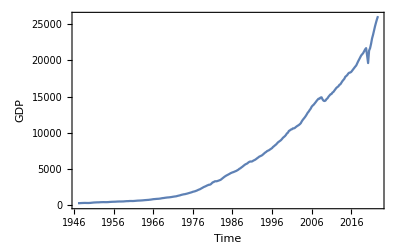

TimeSeries[…]

TimeSeriesModel[…]

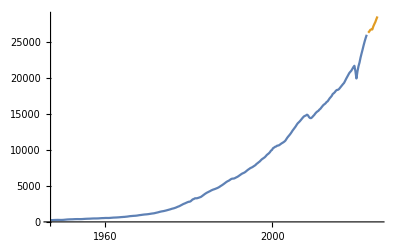

```mathematica
whole2=preprocessedData;
{trainer2,tester2}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->True];
DateListPlot[TimeSeries[trainer2],FrameLabel->{"Time","GDP"}]
ts=TimeSeries[trainer2];
resampledTS=TimeSeriesResample[ts]
tsm=TimeSeriesModelFit[resampledTS]
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10}]}] (*the next 5 steps*)
```

## Using Neural Networks

```mathematica
whole2=preprocessedData;
{trainer2,tester2}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->True];(*And the date values are stored in the first element of each example*)

(*Preprocessing to convert date objects to numerical values*)preprocessedTrain=Transpose[{DateValue[#[[1]],"UnixTimestamp"],#[[2]]}&/@trainer3];
preprocessedTest=Transpose[{DateValue[#[[1]],"UnixTimestamp"],#[[2]]}&/@tester3];

First[preprocessedTrain]

net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Sigmoid],LinearLayer[10],BatchNormalizationLayer[],ElementwiseLayer[Sigmoid],LinearLayer[1]},"Input"->1,"Output"->"Scalar"]

results=NetTrain[net,preprocessedTrain,All,ValidationSet->preprocessedTest,Method->"Adam"]

{trainedNet,valLosses}=results[{"TrainedNet","ValidationLossList"}]
Min[valLosses]

trainedNet[{DateValue[trainer3[[1,1]],"UnixTimestamp"]}]

p=Predict[preprocessedTrain,PerformanceGoal->"Quality"]
pm=PredictorMeasurements[p,preprocessedTest,"MeanSquare"]
```

NetTrain::invtdata: Training data should be an association of lists, or a rule from input to output examples.

$Failed

NetExtract::arg1: First argument $Failed should be a net, NetEncoder, or NetDecoder.

$Failed[ValidationLoss]

$Failed[ValidationLoss]